```mathematica
integrate[h_,n_,L_,y0_]:=
(
f[t_, y_]:=-L(y-Cos[30t])-30Sin[30t];
ys={y0};
For[i=0,i<n,i+=1,
current = ys[[-1]];
k1 = 1/(1+h*L) f[(i+1)*h , current];
k2 = 1/(1+h*L)( f[(i+2)*h , current]-h*L*k1);
k3 = 1/(1+h*L) (f[(i+1)*h , current]-(h*L)/2 k1+(h*L)/2 k2);
k4 = 1/(1+h*L)( f[(i+2)*h , current]+h*L(-k1+k2-k3));
AppendTo[ys,current+h*(k1-k2+k3+k4)];
];
(*result=Table[NumberForm[ys[[j+1]]-(E^(-L*h*2*j)+Cos[30*h*2*j]),3],{j,0,n}];
result=Insert[result, h,1];
result =Insert[result, L, 1];
Return[result];*)
ListPlot[Table[{i*h,ys[[i+1]]},{i,0,n}],Joined->True]
);
```

```mathematica
Grid[Table[integrate[.1,10,10^k,2],{k,1,5}],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

10 | 0.001 | 0. | -3.81×10^-6 | 0.00181 | 0.00545 | 0.0109 | 0.0181 | 0.0271 | 0.0379 | 0.0502 | 0.0642 | 0.0796
100 | 0.001 | 0. | 0.000511 | 0.00287 | 0.00723 | 0.0137 | 0.0224 | 0.0332 | 0.0463 | 0.0616 | 0.0791 | 0.0987
1000 | 0.001 | 0. | 0.0209 | 0.00898 | 0.00987 | 0.0171 | 0.0278 | 0.0412 | 0.0572 | 0.0755 | 0.0962 | 0.119
10000 | 0.001 | 0. | -0.0327 | 0.00426 | 0.009 | 0.0175 | 0.0286 | 0.0423 | 0.0584 | 0.077 | 0.0979 | 0.121
100000 | 0.001 | 0. | -0.0048 | 0.00317 | 0.00898 | 0.0174 | 0.0285 | 0.0422 | 0.0583 | 0.0768 | 0.0977 | 0.121

```mathematica
Grid[Table[integrate[.01,10,10^k,2],{k,1,5}],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

10 | 0.01 | 0. | -0.00436 | 0.143 | 0.321 | 0.369 | 0.158 | -0.353 | -1.09 | -1.87 | -2.48 | -2.72
100 | 0.01 | 0. | 0.0172 | 0.241 | 0.553 | 0.761 | 0.71 | 0.338 | -0.297 | -1.03 | -1.65 | -1.96
1000 | 0.01 | 0. | -0.0326 | 0.265 | 0.597 | 0.817 | 0.773 | 0.402 | -0.238 | -0.984 | -1.62 | -1.94
10000 | 0.01 | 0. | -0.00477 | 0.26 | 0.591 | 0.809 | 0.764 | 0.393 | -0.246 | -0.99 | -1.62 | -1.95
100000 | 0.01 | 0. | -0.000495 | 0.259 | 0.59 | 0.808 | 0.763 | 0.392 | -0.247 | -0.991 | -1.62 | -1.95

```mathematica
Grid[Table[integrate[.001,10,10^k,2],{k,1,5}],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

10 | 0.001 | 0. | -3.81×10^-6 | 0.00181 | 0.00545 | 0.0109 | 0.0181 | 0.0271 | 0.0379 | 0.0502 | 0.0642 | 0.0796
100 | 0.001 | 0. | 0.000511 | 0.00287 | 0.00723 | 0.0137 | 0.0224 | 0.0332 | 0.0463 | 0.0616 | 0.0791 | 0.0987
1000 | 0.001 | 0. | 0.0209 | 0.00898 | 0.00987 | 0.0171 | 0.0278 | 0.0412 | 0.0572 | 0.0755 | 0.0962 | 0.119
10000 | 0.001 | 0. | -0.0327 | 0.00426 | 0.009 | 0.0175 | 0.0286 | 0.0423 | 0.0584 | 0.077 | 0.0979 | 0.121
100000 | 0.001 | 0. | -0.0048 | 0.00317 | 0.00898 | 0.0174 | 0.0285 | 0.0422 | 0.0583 | 0.0768 | 0.0977 | 0.121

```mathematica
Grid[Table[integrate[.0001,10,10^k,2],{k,1,5}],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

10 | 0.0001 | 0. | -3.68×10^-9 | 0.000018 | 0.0000541 | 0.000108 | 0.00018 | 0.000271 | 0.000379 | 0.000506 | 0.00065 | 0.000813
100 | 0.0001 | 0. | 7.54×10^-7 | 0.0000197 | 0.0000571 | 0.000113 | 0.000188 | 0.000281 | 0.000394 | 0.000526 | 0.000677 | 0.000848
1000 | 0.0001 | 0. | 0.000544 | 0.000911 | 0.00116 | 0.00132 | 0.00144 | 0.00153 | 0.00161 | 0.0017 | 0.0018 | 0.00193
10000 | 0.0001 | 0. | 0.0209 | 0.00613 | 0.00142 | 0.00043 | 0.000328 | 0.000426 | 0.000584 | 0.000775 | 0.000993 | 0.00124
100000 | 0.0001 | 0. | -0.0327 | 0.0011 | 0.0000557 | 0.000178 | 0.000289 | 0.000429 | 0.000596 | 0.000789 | 0.00101 | 0.00126

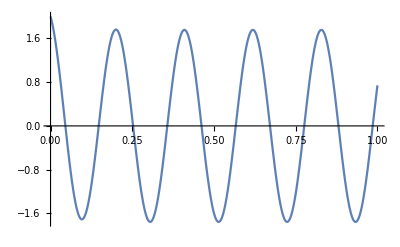
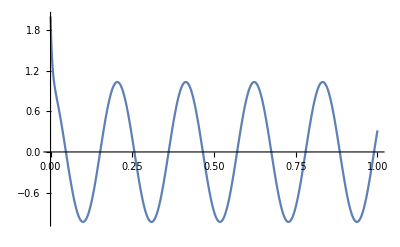
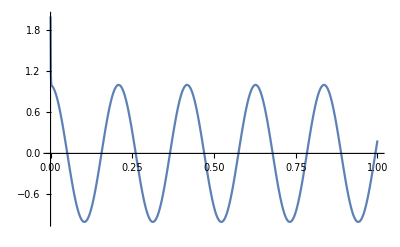
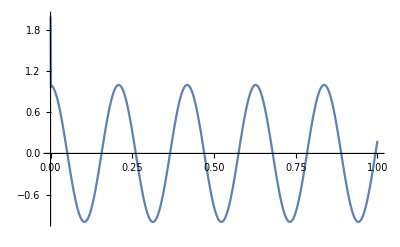
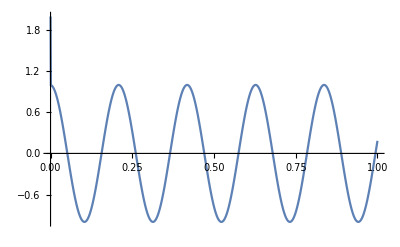
L=10
-Graphics-L=100
-Graphics-L=1000
-Graphics-L=10000
-Graphics-L=100000
-Graphics-

```mathematica
Row@Table[Column[{StringJoin["L=",ToString[10^k]],integrate[.001,1/.001,10^k,2]}],{k,1,5}]
```

```mathematica
85^2
```

7225

```mathematica
83^2+2*169
```

7227

```mathematica
(85-6*13)^2+36
```

85

```mathematica
7^2+6^2
```

85

```mathematica
47^2+13^2
```

2378

```mathematica
7^2+21^2
```

490

```mathematica
19^2+2^2
```

365

```mathematica
9^2+36
```

117

```mathematica
16+64
```

80